```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jevin/code/ece437/midterm_report

```mathematica
ins=160+29+278
pcyc=411+62+676
scyc=205+31+319
pcpi=pcyc/ins//N
scpu=scyc/ins//N
```

467

1149

555

2.46039

1.18844

{20500,10250,4100,1740,870,98}

{41100,20550,8220,4110,1695,66}

{{20500.,41100.},{10250.,20550.},{4100.,8220.},{1740.,4110.},{870.,1695.},{98.,66.}}

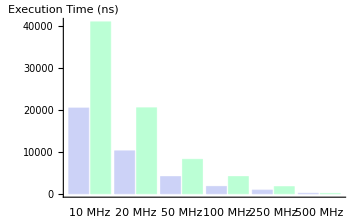
-Graphics--Graphics- | Single-cycle
-Graphics- | Pipelined

```mathematica
tcl={100,50,20,10,5,2};
fscyc={205,205,205,174,174,49};
fstime=tcl*fscyc
fpcyc={411,411,411,411,339,33};
fptime=tcl*fpcyc
Transpose[{fstime,fptime}]//N
fchart=BarChart[Transpose[{fstime,fptime}],ChartLabels->{{"10 MHz","20 MHz","50 MHz","100 MHz","250 MHz","500 MHz"},None},ChartLegends->{"Single-cycle","Pipelined"},AxesLabel->{None,"Execution Time (ns)"},PerformanceGoal->"Quality",ImageSize->Medium]
Export["fib_chart.pdf", fchart];
```

{3100,1550,620,100,50,20}

{6200,3100,1240,620,75,30}

{{3100.,6200.},{1550.,3100.},{620.,1240.},{100.,620.},{50.,75.},{20.,30.}}

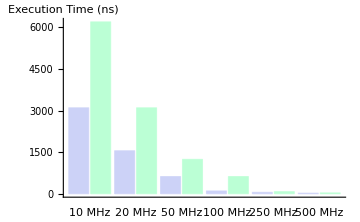
-Graphics--Graphics- | Single-cycle
-Graphics- | Pipelined

```mathematica
mscyc={31,31,31,10,10,10};
mstime=tcl*mscyc
mpcyc={62,62,62,62,15,15};
mptime=tcl*mpcyc
Transpose[{mstime,mptime}]//N
mchart=BarChart[Transpose[{mstime,mptime}],ChartLabels->{{"10 MHz","20 MHz","50 MHz","100 MHz","250 MHz","500 MHz"},None},ChartLegends->{"Single-cycle","Pipelined"},AxesLabel->{None,"Execution Time (ns)"},PerformanceGoal->"Quality",ImageSize->Medium]
Export["mult_chart.pdf", mchart];
```

```mathematica
sscyc={319,319,319,127,127,73};
sstime=tcl*sscyc
spcyc={676,676,676,676,478,49};
sptime=tcl*spcyc
Transpose[{sstime,sptime}]//N
schart=BarChart[Transpose[{sstime,sptime}],ChartLabels->{{"10 MHz","20 MHz","50 MHz","100 MHz","250 MHz","500 MHz"},None},ChartLegends->{"Single-cycle","Pipelined"},AxesLabel->{None,"Execution Time (ns)"},PerformanceGoal->"Quality",ImageSize->Medium]
Export["search_chart.pdf", schart];
```